## Basic Function Generating: Develop foundational functions to facilitate the execution of the scripts.

```mathematica
(*Font Setting*)
style1={FontFamily->"Times New Roman",FontSize->12,Bold};
style2={FontFamily->"Times New Roman",FontSize->10};
(*Triangular Waveform Synthesis*)
```

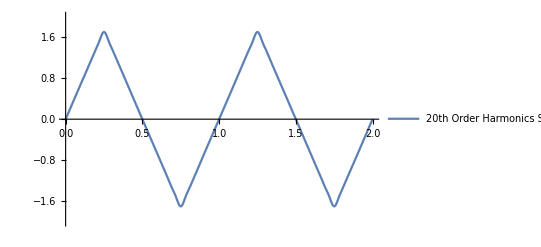

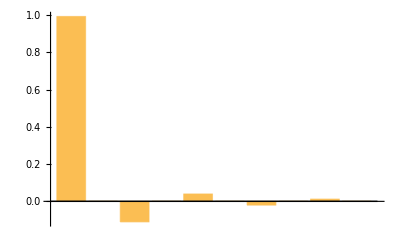

0.999999

```mathematica
Fsin[k_,t_]=Piecewise[{{√2 Sin[2π k t],k≠0},{1,k==0}}];
BkTri[k_,d_]=Piecewise[{{0,k==0},{√6*(-1)^(k+1)Sin[k(1-d)π]/(k^2(d-d^2)π^2),k≠0}}];BkTriWave[t_,d_]:=∑_(k=0)^20 BkTri[k,d]×Fsin[k,t];
Plot[BkTriWave[t,1/2],{t,0,2},PlotRange->{-2,2},PlotLegends->{"20th Order Harmonics Synthesis"}]

BarChart[Table[BkTri[k,1/2],{k,1,10}]]
N[Sqrt[Total[Table[BkTri[k,1/2]^2,{k,1,40}]]]]
```

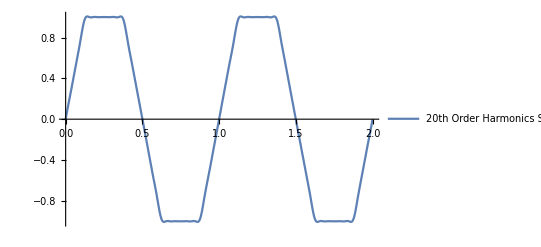

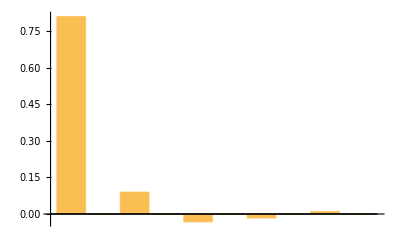

0.816496

```mathematica
(*Trapezoidal Waveform Synthesis*)
BkTrape[k_,d_]:=Piecewise[{{0,Mod[k,2]==0},{√2 Sin[2 k π d]/(d k^2 π^2),Mod[k,2]==1}}];
BkTrapeWave[t_,d_]:=∑_(k=0)^20 BkTrape[k,d]×Fsin[k,t]
Plot[BkTrapeWave[t,0.125],{t,0,2},PlotLegends->{"20th Order Harmonics Synthesis"}]
BarChart[Table[BkTrape[k,0.125],{k,1,10}]]
N[Sqrt[Total[Table[BkTrape[k,0.125]^2,{k,1,40}]]]]
```

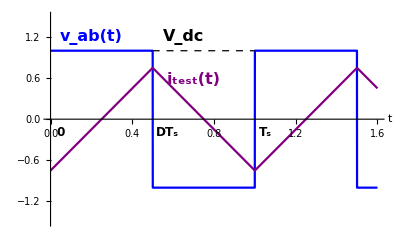

-Graphics-

```mathematica
(*Square Waveform Synthesis*)
Vsq[t_]=Piecewise[{{1,0≤Mod[ t,1]<1/2},{-1,1/2≤Mod[ t,1]≤1}}];
Isq[t_]=Piecewise[{{Mod[t,1]-1/4,0≤Mod[ t,1]<1/2},{Mod[1-t,1]-1/4,1/2≤Mod[ t,1]≤1}}];
SQWAVEPLOT=Plot[{Vsq[t],3Isq[t]},{t,0,1.6},Exclusions->None,PlotRange->{-1.5,1.5},AxesStyle->Directive[Black],Ticks->{None,None},AxesLabel->{Style["t",Bold,FontFamily->"Times New Roman",FontSize->16],Style["",Bold,style1]},PlotStyle->{Blue,Purple},Epilog->{Text[Style["0",FontFamily->"Times New Roman",Italic,Bold,FontSize->12],{0+0.05,-0.2}],Text[Style["T_s",FontFamily->"Times New Roman",Italic,Bold,FontSize->12],{1+0.05,-0.2}],Text[Style["DT_s",FontFamily->"Times New Roman",Italic,Bold,FontSize->12],{0.5+0.07,-0.2}],{Lighter[Black,0.1],Dashed,Line[{{0.5,1},{1,1}}]},Text[Style["V_dc",FontFamily->"Times New Roman",Italic,Bold,Black,FontSize->16],{0.60+0.05,1.2}],
Text[Style["v_ab(t)",FontFamily->"Times New Roman",Italic,Bold,Blue,FontSize->16],{0.2,1.2}],Text[Style["i_test(t)",FontFamily->"Times New Roman",Italic,Bold,Purple,FontSize->16],{0.7,0.58}]}]
RESISPLOT=ListLogPlot[{Table[{k,Abs[√k]},{k,0.1,20,0.1}],Table[(Abs[BkTri[k,1/2]])^2*Abs[√k],{k,1,20}],Table[Abs[BkTri[k,1/2]],{k,1,20}]},PlotRange->{10^-5,10},Joined->{True,False,False},PlotMarkers->{"","■","•",""},AxesLabel->{Style["n^th Order",style1],Style["Normalized\nValue",style1]},AxesStyle->Directive[Black],PlotStyle->{Darker[Green,0.5],Darker[Red,0.2],Lighter[Blue,0.4]},FillingStyle->Lighter[Blue,0.6],GridLines->{{},Table[10^i,{i,-5,1}]},GridLinesStyle->{Directive[Gray,Thin,Line],Directive[Lighter[Gray,0.5],Line,Thin]},Ticks->{Table[2i-1,{i,1,10}],Flatten[{Table[10.0^i,{i,-6,3,1}]}]},ImageSize->Medium,Epilog->{Text[Style["AC Resistance",FontFamily->"Times New Roman",Italic,Darker[Green,0.5],Bold,FontSize->12],{15,0.2}],Text[Style["Harmonic Component",FontFamily->"Times New Roman",Italic,Lighter[Blue,0.3],Bold,FontSize->12],{15,-3.5}],Text[Style["Loss of n^th Order",FontFamily->"Times New Roman",Italic,Darker[Red,0.2],Bold,FontSize->12],{15,-7.5}]}]
```

```mathematica
(*Error Estimation of Using Triangular Resistance at D=0.5 as the Sinusoidal Value*)
ESTERROR=N[Total[Table[(Abs[BkTri[k,1/2]])^2*Abs[√k],{k,1,20}]]/Total[Table[(Abs[BkTri[k,1/2]])^2*1,{k,1,20}]]]-1
```

0.0121963

## Measured Data of the Impedance Analyzer: Extracting from CSV files.

```mathematica
Ldata[IndName_]:=Import["D:WorkZone/Measurements of the Impedance Analyzer/"<>ToString[IndName]<>".csv","Data"][[5;;]]
(*Calculation of the Sinusoidal/ Tringular / Trapezoidal Resistances*)
SinR[IndName_]:=Ldata[IndName][[10*1+1]][[3]]*1000;
TriR[IndName_,duty_]:=Total[Table[BkTri[k,duty]^2*Ldata[IndName][[10*k+1]][[3]]*1000,{k,1,10}]];
TrapeR[IndName_,duty_]:=Total[Table[BkTrape[k,duty]^2/(∑_(k=0)^20 (BkTrape[k,duty]^2))*Ldata[IndName][[10*k+1]][[3]]*1000,{k,1,10}]];
```

```mathematica
(*Example, A14 Inductor, Measured Inductances and Resistances at 100 kHz to 5 MHz, Unit transformed From (H,Ω) to (μH,mΩ)*)
A14IMP=Ldata[A14][[2;;51]][[All,{1,3}]].{{1/1000000,0},{0,1000}}
(*Example, A14 Inductor, Simulated Inductances and Resistances at 100 kHz to 5 MHz*)
A14SIMU=Import["D:WorkZone/Measurements of the Impedance Analyzer/A14SIMU.csv","Data"][[2;;51]][[All,{2,3}]]
```

{{0.1,33.3662},{0.2,45.3119},{0.3,54.232},{0.4,61.6685},{0.5,68.2285},{0.6,73.8334},{0.7,79.3965},{0.8,84.3524},{0.9,89.0827},{1.,93.6362},{1.1,97.846},{1.2,101.827},{1.3,105.611},{1.4,109.376},{1.5,113.772},{1.6,118.316},{1.7,121.628},{1.8,125.272},{1.9,128.692},{2.,131.764},{2.1,135.394},{2.2,138.728},{2.3,141.803},{2.4,144.653},{2.5,147.787},{2.6,150.519},{2.7,153.349},{2.8,156.426},{2.9,159.05},{3.,161.967},{3.1,164.599},{3.2,167.224},{3.3,169.99},{3.4,172.65},{3.5,175.429},{3.6,177.813},{3.7,180.172},{3.8,182.793},{3.9,185.484},{4.,187.834},{4.1,190.063},{4.2,192.744},{4.3,194.696},{4.4,197.1},{4.5,199.584},{4.6,201.863},{4.7,204.329},{4.8,206.352},{4.9,208.65},{5.,210.937}}

{{0.1,33.6076},{0.2,44.356},{0.3,53.1461},{0.4,60.7309},{0.5,67.4945},{0.6,73.6546},{0.7,79.3478},{0.8,84.666},{0.9,89.6747},{1,94.4221},{1.1,98.9452},{1.2,103.273},{1.3,107.429},{1.4,111.432},{1.5,115.297},{1.6,119.039},{1.7,122.668},{1.8,126.193},{1.9,129.624},{2,132.967},{2.1,136.228},{2.2,139.414},{2.3,142.53},{2.4,145.58},{2.5,148.567},{2.6,151.496},{2.7,154.37},{2.8,157.192},{2.9,159.964},{3,162.69},{3.1,165.371},{3.2,168.009},{3.3,170.607},{3.4,173.167},{3.5,175.689},{3.6,178.176},{3.7,180.629},{3.8,183.049},{3.9,185.438},{4,187.797},{4.1,190.126},{4.2,192.428},{4.3,194.702},{4.4,196.951},{4.5,199.174},{4.6,201.373},{4.7,203.548},{4.8,205.701},{4.9,207.831},{5,209.94}}

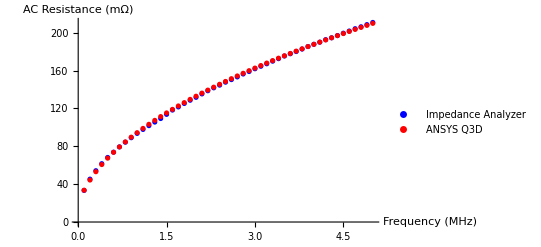

```mathematica
ImpSimuComparision=ListPlot[{A14IMP,A14SIMU},AxesLabel->{Style["Frequency\n(MHz)",style1,Bold],Style["AC Resistance\n(mΩ)",style1,Bold]},PlotStyle->{Blue,Red},GridLines->{{},{}},GridLinesStyle->{Directive[Gray,DotDashed,Thin],Directive[Gray,DotDashed,Thin]},LabelStyle->Directive["Times New Roman",Black],PlotLegends->Placed[{Style["Impedance Analyzer",style1,Bold],Style["ANSYS Q3D",style1,Bold]},{0.7,0.48}]]
```

## Measured Data of the Proposed Method: Extracting from CSV files.

```mathematica
LossData[IndName_]:=Import["D:WorkZone/Measurements of the Proposed Method/T1"<>ToString[IndName]<>"_Duty50%_Freq1MHz.xls","Data"][[2;;]][[All,{4,1,2}]]
(*Calculation of the Inverter Loss*)

InverterLoss[IndName_]:=(LossData[IndName]-((LossData[IndName].DiagonalMatrix[{1,0,0}])^2*(TriR[IndName,0.5])).{{0,0,1},{0,1,0},{1,0,0}});

(*Example, Inverter Loss When A14 Inductor is connected*)
InverterLoss[A14]

(*Fitting DataSet, Using Inductors A0,A5,A6-A40...*)
dataFitT1=Flatten[{Table[InverterLoss[ToExpression["A"<>ToString[Np]]],{Np,6,40,2}],Table[InverterLoss[ToExpression["A"<>ToString[Np]]],{Np,{0,5,9,11,56,58}}],Table[InverterLoss[ToExpression["LA"<>ToString[Np]]],{Np,{10,15}}]},2]
```

{{0.2,1.62,4.73671},{0.25,2.03,7.57524},{0.3,2.44,11.1591},{0.35,2.85,15.3943},{0.4,3.25,20.0809},{0.45,3.68,25.8587},{0.5,4.08,32.172},{0.55,4.5,39.0685},{0.6,4.91,46.8474},{0.65,5.32,55.2227},{0.7,5.74,64.3552},{0.75,6.15,74.1702},{0.8,6.56,84.7704},{0.85,6.96,95.862},{0.9,7.38,107.955},{0.95,7.79,120.553},{1.,8.2,133.782},{1.05,8.62,148.186},{1.1,9.03,162.876},{1.15,9.44,178.83},{1.2,9.85,195.073},{1.25,10.26,212.876},{1.3,10.68,230.773},{1.35,11.09,249.457},{1.4,11.51,269.205},{1.45,11.92,289.904},{1.5,12.32,310.604},{1.55,12.74,333.002},{1.6,13.15,355.712},{1.65,13.56,379.82},{1.7,13.97,404.383},{1.75,14.39,429.977},{1.8,14.8,455.772},{1.85,15.21,482.388},{1.9,15.62,510.08},{1.95,16.04,539.008},{2.,16.44,568.147},{2.05,16.85,597.509},{2.1,17.28,628.608},{2.15,17.69,660.349},{2.2,18.11,693.183},{2.25,18.52,725.944},{2.3,18.94,760.27},{2.35,19.35,794.639},{2.4,19.77,830.231},{2.45,20.17,865.858},{2.5,20.59,902.633},{2.55,21.,939.537},{2.6,21.41,977.597},{2.65,21.82,1016.04},{2.7,22.25,1057.18},{2.75,22.66,1096.76},{2.8,23.07,1137.55},{2.85,23.48,1179.81},{2.9,23.9,1221.71},{2.95,24.31,1265.15},{3.,24.73,1309.99},{3.05,25.15,1353.67},{3.1,25.56,1398.05},{3.15,25.97,1444.26},{3.2,26.37,1489.96},{3.25,26.79,1537.31},{3.3,27.21,1585.06},{3.35,27.63,1634.87},{3.4,28.04,1684.13},{3.45,28.45,1734.16},{3.5,28.87,1785.51},{3.55,29.28,1837.39},{3.6,29.69,1889.78},{3.65,30.1,1943.7},{3.7,30.52,1997.7},{3.75,30.93,2051.8},{3.8,31.34,2107.77},{3.85,31.76,2166.2},{3.9,32.18,2223.26},{3.95,32.59,2281.31},{4.,33.,2339.77},{4.05,33.43,2401.75},{4.1,33.82,2460.87},{4.15,34.24,2522.65},{4.2,34.67,2586.61},{4.25,35.07,2647.6},{4.3,35.49,2713.06},{4.35,35.9,2777.68},{4.4,36.31,2842.72},{4.45,36.73,2911.87},{4.5,37.15,2980.11},{4.55,37.56,3048.99},{4.6,37.98,3118.51},{4.65,38.39,3189.6},{4.7,38.8,3260.62},{4.75,39.23,3333.17},{4.8,39.64,3404.58},{4.85,40.06,3478.65},{4.9,40.46,3553.75},{4.95,40.88,3628.34},{5.,41.29,3703.95},{0.,0.,0.}}

{{0.2,0.84,6.70363},{0.25,1.05,10.6015},{0.3,1.27,15.4387},{0.35,1.48,20.935},{0.4,1.69,27.3075},{0.45,1.91,34.4552},{0.5,2.13,42.7182},{0.55,2.34,51.6293},{0.6,2.56,61.3507},2047,{4.65,12.63,3134.61},{4.7,12.76,3202.39},{4.75,12.9,3278.65},{4.8,13.03,3351.},{4.85,13.17,3413.23},{4.9,13.3,3481.83},{4.95,13.44,3556.23},{5.,13.58,3630.63},{0.,0.,0.}}
 |  |  |  |

## Fitting Performance of Artificial Neural Network & Analytical Model

```mathematica
(*Fitting DataSet Mapping*)
Traindata=Table[{dataFitT1[[i]][[1]],dataFitT1[[i]][[2]]}->dataFitT1[[i]][[3]],{i,1,Length[dataFitT1]}];
(*Neural Network Structure*)
net=NetChain[{32,Tanh,32,1}];
lossNet=NetGraph[<|"net"->net,"loss"->ThreadingLayer[Sqrt[(#1-#2)^2+1]&]|>,{{"net",NetPort["Target"]}->"loss"->NetPort["Loss"]}];
(*Setting Validation DataSet to 50%*)
trainedLossNet=NetTrain[lossNet,Traindata,Method->{"ADAM","LearningRate"->0.001},LossFunction->"Loss",BatchSize->32,MaxTrainingRounds->7200,ValidationSet->Scaled[0.5]]
(*Training Process*)
p1=NetExtract[trainedLossNet,"net"]
p=p1;
```

NetGraph[<>]

NetChain[<>]

```mathematica
(*Analytical Model Structure*)
model=a1*Vdc^2+a2*Irms+a3*Vdc+a4*Vdc*Log[Irms+10^-12]+a5*Vdc*Log[Vdc+10^-12]+a6*Irms*Log[Irms+10^-12]+Irms^2*(a7)+a8;
fit1=FindFit[dataFitT1,{model},{a1,a2,a3,a4,a5,a6,a7,a8},{Irms,Vdc}]
Show[Plot3D[model/.fit1,{Irms,0.2,5},{Vdc,1,70},PlotRange->All],ListPointPlot3D[dataFitT1,PlotStyle->Directive[PointSize[Medium],Blue]]]
```

{a1→0.0538612,a2→98.6293,a3→-41.3168,a4→-19.2774,a5→14.2318,a6→-62.4724,a7→177.362,a8→-43.3414}

-Graphics3D-

```mathematica
(*Performance Check DataSet*)
dataCheck=
Flatten[{Table[InverterLoss[ToExpression["A"<>ToString[Np]]],{Np,6,36,4}],Table[InverterLoss[ToExpression["A"<>ToString[Np]]],{Np,{9,5,11}}],Table[InverterLoss[ToExpression["LA"<>ToString[Np]]],{Np,{10}}]},2];
CheckData=Table[{{dataCheck[[i]][[1]],dataCheck[[i]][[2]]},dataCheck[[i]][[3]]},{i,1,Length[dataCheck]}];
(*Error Comparision in mW*)
FitPlot=ListPlot[{Transpose[{CheckData[[All,1]][[All,1]],p1[CheckData[[All,1]]][[All,1]]-dataCheck[[All,3]]}],Transpose[{dataCheck[[All,1]],(model/.fit1/.{Irms->dataCheck[[All,1]],Vdc->dataCheck[[All,2]]})-dataCheck[[All,3]]}]},PlotRange->{{0,5},{-150,150}},PlotLegends->Placed[{Style["Neural Network",style1,Bold],Style["Model in [26]",style1,Bold]},{0.65,0.12}],PlotStyle->{Lighter[Blue,0.2],Darker[Red,0.2]},AxesLabel->{},PlotMarkers->"⋄",GridLinesStyle->{Directive[Gray,DotDashed,Thin],Directive[Gray,DotDashed,Thin]},LabelStyle->Directive[Black],Ticks->Automatic,Frame->True,AxesStyle->Black,Epilog->{Text[Style["Fitting Error\n(mW)",style1,Bold],{0.6,120}],Text[Style["I_test(A)",style1,Bold],{4.6,-130}]},ImageSize->Medium]
```

-Graphics-

```mathematica
(*Error Comparision in Percentage*)
FitPlotPercentage=ListPlot[{Transpose[{CheckData[[All,1]][[All,1]],100(p1[CheckData[[All,1]]][[All,1]]-dataCheck[[All,3]])/(dataCheck[[All,3]]+10^-12)}],Transpose[{dataCheck[[All,1]],100((model/.fit1/.{Irms->dataCheck[[All,1]],Vdc->dataCheck[[All,2]]})-dataCheck[[All,3]])/(dataCheck[[All,3]]+10^-12)}]},PlotRange->{{0,5},{-20,20}},PlotLegends->Placed[{Style["Neural Network",style1,Bold],Style["Model in [26]",style1,Bold]},{0.75,0.25}],PlotStyle->{Lighter[Blue,0.2],Darker[Red,0.2]},AxesLabel->{},PlotMarkers->"⋄",GridLinesStyle->{Directive[Gray,DotDashed,Thin],Directive[Gray,DotDashed,Thin]},LabelStyle->Directive[Black],Ticks->Automatic,Frame->True,AxesStyle->Black,Epilog->{Text[Style["Fitting Error\n(%)",style1,Bold,Background->White],{0.6,16}],Text[Style["I_test(A)",style1,Bold],{4.6,-16}]},ImageSize->Medium]
```

-Graphics-

```mathematica
Export["D:WorkZone/FitPlot.tif",FitPlot,ImageResolution->300]
Export["D:WorkZone/FitPlotPercentage.tif",FitPlotPercentage,ImageResolution->300]
```

D:WorkZone/FitPlot.tif

D:WorkZone/FitPlotPercentage.tif

## Solve Basic Equations of the Proposed Method For the Transformer Testing

```mathematica
(*Calculation of the Measured Resistance*)

RCAL[RMeasure_]:=(RMeasure[[All,3]]-Table[p[{RMeasure[[All,1]][[i]],RMeasure[[All,2]][[i]]}][[1]],{i,1,Length[RMeasure[[All,1]]]}])/RMeasure[[All,1]]^2
(*Equation of Multiple Measurements*)
R1=.;R2=.;R3=.;
Eq1=R1==Rp+Rm;
Eq2=R2==Rs+1/k^2 Rm;
Eq3=R3==Rp+((k+1)^2 Rm)/k^2+Rs;
Sol=FullSimplify[Solve[Eq1&&Eq2&&Eq3,{Rp,Rs,Rm}]]
(*Solutions in Matrix Form, for Positive Connection and Negtive one*)
SolPos=FullSimplify[Inverse[{{1,0,1},{0,1,1/k^2},{1,1,(k+1)^2/k^2}}]]
SolNeg=FullSimplify[Inverse[{{1,0,1},{0,1,1/k^2},{1,1,(k-1)^2/k^2}}]];
```

{{Rp→1/2 ((2+k) R1+k (R2-R3)),Rs→(R1+R2+2 k R2-R3)/(2 k),Rm→-1/2 k (R1+R2-R3)}}

{{(2+k)/2,k/2,-k/2},{1/(2 k),1+1/(2 k),-1/(2 k)},{-k/2,-k/2,k/2}}

```mathematica
(*CALCULATING ERRORS OF DIFFERENT TURNS-RATIO*)
ErrorEstimaton=FullSimplify[Sqrt[((SolPos)^2).({1,1,1})^2] *ΔR]
```

{1/2 √(4+k (4+3 k)) ΔR,1/2 √((3+4 k (1+k))/k^2) ΔR,1/2 √3 √(k^2) ΔR}

## Verification Air-core Transformer 16:16

```mathematica
(*Measured Resistance of Impedance Analyzer in mΩ, (R1,R2,R3)*)
Tr1616IMP={TriR[TRANSFORMER1616WINDING1,0.5],TriR[TRANSFORMER1616WINDING2,0.5],TriR[TRANSFORMER1616WINDINGSERIES,0.5]}
```

{111.315,113.922,260.177}

```mathematica
(*Calculated Resistance of Impedance Analyzer in mΩ, (Rp,Rs,Rm)*)
Tr1616IMPFIN=SolPos.Tr1616IMP/.{k->1}
```

{93.8451,96.4518,17.4701}

```mathematica
(*Measured Resistance of the Proposed Method in mΩ, (R1,R2,R3)*)
Tr1616=Import["D:WorkZone/Measurements of the Proposed Method/T1TR1616_01_Duty50%_Freq1MHz.xls","Data"][[2;;49*3+1]][[All,{4,1,2}]];

Tr1616TEST=RCAL/@Table[Tr1616[[i;;;;3]],{i,1,3}]
```

{{119.065,142.002,133.325,124.22,117.634,114.76,113.061,112.913,112.922,113.064,113.402,113.611,113.817,113.771,113.784,113.745,113.874,113.931,114.123,114.2,114.285,114.566,114.673,114.864,114.975,115.102,115.265,115.421,115.438,115.462,115.471,115.535,115.443,115.398,115.298,115.22,115.081,115.023,114.967,114.894,114.79,114.644,114.581,114.634,114.614,114.589,114.658,114.694,114.889},{125.981,146.503,135.736,126.327,120.066,116.566,115.081,114.53,114.265,114.759,115.092,115.243,115.463,115.608,115.572,115.532,115.668,115.708,115.791,115.857,116.137,116.258,116.475,116.581,116.741,116.895,117.103,117.218,117.181,117.202,117.184,117.258,117.183,117.14,117.079,116.985,116.894,116.846,116.881,116.665,116.553,116.511,116.421,116.449,116.411,116.365,116.423,116.484,116.683},{1248.39,826.174,565.405,424.07,351.155,309.477,284.741,273.753,263.591,259.465,258.788,259.697,263.01,266.274,269.982,271.728,275.284,276.255,276.86,277.639,277.257,276.829,276.57,275.334,274.82,273.752,272.956,271.758,270.709,270.431,269.803,269.427,269.068,268.723,268.666,268.475,268.365,268.171,268.156,267.777,267.555,267.083,267.011,266.738,266.645,266.229,265.831,266.019,265.745}}

```mathematica
(*Calculated Resistance of Proposed Method in mΩ, (Rp,Rs,Rm)*)
Tr1616TESTFIN=SolPos.Tr1616TEST/.{k->1}
```

{{-382.606,-126.832,-14.8473,37.4583,60.9054,75.6843,84.761,89.7587,94.7197,97.2426,98.2545,98.1905,96.9529,95.323,93.4708,92.5198,91.0029,90.6229,90.6493,90.4093,90.8679,91.5635,91.9621,92.9201,93.4231,94.2247,94.9708,95.8624,96.393,96.5777,96.8976,97.2176,97.2228,97.3059,97.1537,97.0844,96.8853,96.8725,96.8125,96.7855,96.6833,96.6802,96.5771,96.807,96.8041,96.9515,97.2829,97.274,97.8018},{-375.691,-122.331,-12.4357,39.5662,63.3375,77.4905,86.7813,91.3757,96.0634,98.9378,99.9447,99.8226,98.5984,97.1608,95.2583,94.3064,92.7973,92.3999,92.3175,92.0661,92.7197,93.2555,93.7638,94.6363,95.1897,96.0179,96.8096,97.6594,98.1359,98.3184,98.6107,98.9412,98.9622,99.0472,98.935,98.8495,98.6983,98.6948,98.7263,98.5557,98.4465,98.5476,98.4171,98.6214,98.6014,98.728,99.0484,99.0635,99.5956},{501.671,268.834,148.172,86.7613,56.7281,39.0756,28.2997,23.1546,18.2019,15.8211,15.1472,15.4209,16.8646,18.4476,20.3133,21.2254,22.8709,23.308,23.4732,23.7909,23.4173,23.0024,22.7111,21.9444,21.5517,20.8774,20.2938,19.559,19.0451,18.8838,18.5736,18.3171,18.2206,18.0925,18.1443,18.1353,18.1954,18.151,18.1544,18.109,18.1064,17.9638,18.0041,17.8274,17.8099,17.6373,17.3749,17.4205,17.0869}}

```mathematica
(*Comparision of Verfication*)
S1=Plot[Tr1616IMPFIN,{i,-0,5.0},PlotStyle->Dashed,PlotRange->{0,120},AxesStyle->Black,TicksStyle->Black,Ticks->Automatic,AxesLabel->{Style["I_m(A)",style1],Style["Resistance\n(mΩ)",style1]},LabelStyle->Directive["Arial",Black]];S2=ListPlot[Table[{Tr1616IMPFIN[[i]]},{i,1,3,1}],DataRange->{0.04,0.08},PlotRange->{0,120},AxesStyle->Black,PlotMarkers->{"●"},PlotLegends->Placed[{Style["R_p",style1],Style["R_s",style1],Style["R_m",style1]},{0.75,0.35}]];
S3=ListPlot[Tr1616TESTFIN[[All,2;;]],DataRange->{0.25,5.0},PlotRange->{0,120},AxesStyle->Black,AxesLabel->{Style["I_test(A)",style1],Style["Resistance\n(mΩ)",style1]},PlotLegends->Placed[{Style["R_p",style1],Style["R_s",style1],Style["R_m",style1]},{0.55,0.35}],LabelStyle->Directive["Arial",Black],PlotMarkers->{"▲"}];
TR1616IMG=Show[{S1,S2,S3},ImageSize->Medium,Prolog->{{EdgeForm[{White,Thin}],Thin,Opacity[0.01],Polygon[{{2.10,24},{3.6,24},{3.6,82},{1.8,82}}]},{Text[Style["Impedance\nAnalyzer",style1],{3.9,75}]},{Text[Style["Proposed\nMethod",style1],{2.8,75}]},{Text[Style["Impedance Analyzer\nMeasurement Range",Darker[Red,0.2],Bold,FontFamily->"Times New Roman",FontSize->12],{1.2,60}]},{EdgeForm[],Lighter[Blue,0.2],Opacity[0],Polygon[{{0,0},{0.1,0},{0.1,130},{0,130}}]},{Red,Dashed,Line[{{0.09,130},{0.09,-0}}]},{Red,Line[{{0.09,40},{0.9,50}}]}}]
```

-Graphics-

```mathematica
Export["D:WorkZone/TR1616IMG.tif",TR1616IMG,ImageResolution->330]
```

D:WorkZone/TR1616IMG.tif

## Verification Air-core Transformer 16:8

```mathematica
(*Measured Resistance of Impedance Analyzer in mΩ, (R1,R2,R3)*)
Tr1608IMP={TriR[TRANSFORMER1608WINDING1,0.5],TriR[TRANSFORMER1608WINDING2,0.5],TriR[TRANSFORMER1608WINDINGSERIES,0.5]}
```

{108.77,76.0258,203.861}

```mathematica
(*Calculated Resistance of Impedance Analyzer in mΩ, (Rp,Rs,Rm)*)
Tr1608IMPFIN=SolPos.Tr1608IMP/.{k->2}
```

{89.7047,71.2595,19.0652}

```mathematica
(*Measured Resistance of the Proposed Method in mΩ, (R1,R2,R3)*)
```

```mathematica
Tr1608=Import["D:WorkZone/Measurements of the Proposed Method/T1TR1608_01_Duty50%_Freq1MHz.xls","Data"][[2;;47*3+1]][[All,{4,1,2}]];
Tr1608TEST=RCAL/@Table[Tr1608[[i;;;;3]],{i,1,3}];
(*Calculated Resistance of Proposed Method in mΩ, (Rp,Rs,Rm)*)

Tr1608TESTFIN=SolPos.Tr1608TEST/.{k->2}
```

{{-483.479,-301.495,-187.882,-110.549,-56.1937,-19.6791,7.17723,27.2891,41.3718,52.461,60.8221,67.0397,71.8591,76.1734,79.5439,82.3269,84.864,86.8775,88.5143,89.946,91.011,91.6882,92.2806,92.2858,92.3627,92.1699,91.8027,91.3128,90.876,90.3197,89.6755,89.2041,88.6866,88.1634,87.6777,87.1987,86.7556,86.7496,86.648,86.4881,86.5761,86.7462,86.8531,87.0864,87.2616,87.5343,87.9118},{-101.335,-50.3205,-16.6549,7.49056,25.2887,37.8925,46.999,53.8096,58.2984,61.5782,63.8288,65.3295,66.2781,67.194,67.8607,68.4162,68.9978,69.4935,69.9631,70.4263,70.8412,71.1215,71.3727,71.4769,71.5372,71.5247,71.4437,71.2988,71.1674,70.9841,70.8161,70.6659,70.553,70.4253,70.3183,70.2515,70.1772,70.2547,70.3349,70.3538,70.462,70.5883,70.684,70.7924,70.8509,70.9964,71.0909},{641.613,467.72,349.028,263.173,199.413,154.709,121.294,95.8114,77.6029,63.5792,53.0519,45.1824,39.2836,34.2292,30.4329,27.2996,24.6568,22.6066,21.0064,19.5578,18.5512,17.8947,17.3357,17.3376,17.2294,17.4086,17.7557,18.2041,18.6143,19.143,19.7202,20.1899,20.6942,21.1994,21.6798,22.1589,22.5912,22.6498,22.7739,23.0066,22.9664,22.8855,22.8793,22.728,22.6191,22.4387,22.1641}}

```mathematica
(*Comparision of Verfication*)
S1=ListPlot[Tr1608TESTFIN[[All,1;;]],DataRange->{0.2,2.5},AxesLabel->{Style["I_test(A)",style1],Style["Resistance\n(mΩ)",style1]},PlotLegends->Placed[{Style["R_p",style1],Style["R_s",style1],Style["R_m",style1]},{0.48,0.35}],LabelStyle->Directive["Arial",Black],PlotMarkers->{"▲"}];
S2=ListPlot[Table[{Tr1608IMPFIN[[i]]},{i,1,3,1}],DataRange->{0.03,0.031},PlotMarkers->{"●"},PlotLegends->Placed[{Style["R_p",style1],Style["R_s",style1],Style["R_m",style1]},{0.86,0.35}]];
S3=Plot[Tr1608IMPFIN,{i,-0,2.5},PlotStyle->Dashed,PlotRange->{0,120},AxesStyle->Black,TicksStyle->Black,Ticks->Automatic,AxesLabel->{Style["I_m(A)",style1],Style["Resistance\n(mΩ)",style1]},LabelStyle->Directive["Arial",Black]];
TR1608IMG=Show[{S3,S2,S1},Prolog->{{EdgeForm[{}],Lighter[Red,0.62],Opacity[0.01],Polygon[{{0.65,23},{2,23},{2,63},{0.65,63}}]},{Text[Style["Impedance\nAnalyzer",style1],{1.76,40}]},{Text[Style["Proposed\nMethod",style1],{0.80,40}]},{Text[Style["Impedance Analyzer\nMeasurement Range",Darker[Red,0.2],FontFamily->"Times New Roman",FontSize->12,Bold],{1,110}]},{EdgeForm[],Lighter[Blue,0.2],Opacity[0],Polygon[{{0,0},{0.05,0},{0.05,130},{0,130}}]},{Red,Line[{{0.05,100},{0.5,110}}]},{Red,Dashed,Line[{{0.05,0},{0.05,130}}]}}]
```

-Graphics-

```mathematica
Export["D:WorkZone/TR1608IMG.tif",TR1608IMG,ImageResolution->330]
```

D:WorkZone/TR1608IMG.tif

## Simulation of PCB Transformer 4:2 without Core

```mathematica
(*ANSYS Maxwell Simulated Loss Data of PCB Transformer without Core , (R1,R2,R3)->(Rp,Rs,Rm)*)
Tr0402SIMU={84.320894,29.639661,146.774868}*2;
Tr0402SIMUFIN=SolPos.Tr0402SIMU/.{k->2}
```

{103.013,42.8722,65.6286}

```mathematica
(*ANSYS Maxwell Simulated Loss Data of PCB Transformer with Core , (R1,R2,R3)->(Rp,Rs,Rm)*)
RDATA=Import["D:WorkZone/Simulations Results/TT.csv","Data"][[2+60*6;;]];
R1=Table[RDATA[[i]][[5]]*1000/((RDATA[[i]][[4]])^2)*2,{i,60*2+1,60*2+47,1}];
R2=Table[RDATA[[i]][[5]]*1000/(2RDATA[[i]][[4]])^2*2,{i,1,47,1}];
R3=Table[RDATA[[i]][[5]]*1000/((2/3 RDATA[[i]][[4]])^2)*2,{i,60+1,60+47,1}];
RTABLE1={R1,R2,R3};

RDATA=Import["D:WorkZone/Simulations Results/WD.csv","Data"][[2+60*6;;]];
R1=Table[RDATA[[i]][[5]]*1000/((RDATA[[i]][[4]])^2)*2,{i,60*2+1,60*2+47,1}];
R2=Table[RDATA[[i]][[5]]*1000/(2RDATA[[i]][[4]])^2*2,{i,1,47,1}];
R3=Table[RDATA[[i]][[5]]*1000/((2/3 RDATA[[i]][[4]])^2)*2,{i,60+1,60*1+47,1}];

RTABLE2={R1,R2,R3};
```

```mathematica
SolPos.RTABLE1/.{k->2}

S1=

ListPlot[SolPos.RTABLE1/.{k->2},DataRange->{0.2,2.5},AxesLabel->{Style["I_m(A)",style1],Style["Resistance\n(mΩ)",style1]},AxesStyle->Black,TicksStyle->Black,PlotLegends->Placed[{Style["R_p",style1],Style["R_s",style1],Style["R_m",style1]},{0.7,0.19}],LabelStyle->Directive["Arial",Black],PlotMarkers->{"◆"}];

S2=

ListPlot[(SolPos.RTABLE2/.{k->2})[[3]],DataRange->{0.2,2.5},AxesLabel->{Style["I_m(A)",style1],Style["Resistance\n(mΩ)",style1]},LabelStyle->Directive["Arial",Black],AxesStyle->Black,TicksStyle->Black,PlotStyle->{Darker[Red,0.2]}];

S3=Plot[Tr0402SIMUFIN,{i,-0.01,2.5},PlotRange->{0,200},PlotLegends->Placed[{Style["R_p",style1],Style["R_s",style1],Style["R_m",style1]},{0.3,0.19}],AxesLabel->{Style["I_m(A)",style1],Style["Resistance\n(mΩ)",style1]},LabelStyle->Directive["Arial",Black]];
SIMU0402=Show[{S1,S2,S3},Epilog->{{Text[Style["R_(w, m)(w/ core)",{Darker[Red,0.2],FontSize->12,Bold,FontFamily->"Times New Roman"}],{2,48}]},{Text[Style["R_(c, m)(w/ core)",{Darker[Black,0.1],FontSize->12,Bold,FontFamily->"Times New Roman"}],{2,66}]},{Text[Style["R_m(w/ core)",{Blend[{Green,Gray},0.85],FontSize->12,Bold,FontFamily->"Times New Roman"}],{2,85}]},{Text[Style["Simulation\nw/ core",style1],{2.2,18}]},{Text[Style["Simulation\nw/o core",style1],{1.2,18}]},{EdgeForm[{}],Opacity[0.01],Polygon[{{0.85,2},{3.99,2},{3.99,36},{0.85,36}}]},{Arrowheads[{-0.03,0.03}],Black,Dashed,Arrow[{{1.5,54},{1.5,76}}]},{Arrowheads[{-0.03,0.03}],Black,Dashed,Arrow[{{2.5,54},{2.5,80}}]},{Black,Line[{{1.5,67},{1.68,66}}]},{Black,Line[{{2.5,67},{2.3,66}}]}}]
```

{{102.68,102.679,102.679,102.678,102.677,102.677,102.677,102.676,102.676,102.675,102.675,102.675,102.674,102.674,102.674,102.674,102.673,102.673,102.672,102.673,102.672,102.672,102.672,102.672,102.671,102.671,102.671,102.671,102.67,102.67,102.67,102.67,102.67,102.669,102.669,102.669,102.669,102.669,102.668,102.668,102.668,102.668,102.668,102.668,102.667,102.667,102.667},{42.5802,42.5804,42.5806,42.5807,42.5808,42.581,42.5811,42.5812,42.5813,42.5814,42.5815,42.5816,42.5817,42.5818,42.5819,42.582,42.582,42.5821,42.5821,42.5823,42.5824,42.5824,42.5825,42.5826,42.5826,42.5827,42.5827,42.5828,42.5829,42.5829,42.583,42.5831,42.5831,42.5832,42.5832,42.5833,42.5833,42.5834,42.5834,42.5835,42.5835,42.5836,42.5836,42.5837,42.5837,42.5838,42.5838},{62.6765,63.637,64.4925,65.2694,65.9851,66.6507,67.2753,67.8651,68.4247,68.9582,69.4686,69.9585,70.4299,70.8847,71.3244,71.7504,72.1636,72.5653,72.956,73.3362,73.7075,74.0702,74.4245,74.7708,75.1101,75.4424,75.7683,76.0878,76.4017,76.7098,77.0127,77.3104,77.6035,77.8918,78.1757,78.4553,78.7309,79.0025,79.2703,79.5345,79.7952,80.0525,80.3066,80.5575,80.8054,81.0503,81.2923}}

-Graphics-

## Verification PCB Transformer 4:2 without Core

```mathematica
(*Measured Resistance of Impedance Analyzer in mΩ, (R1,R2,R3)*)
```

```mathematica
Tr0402IMP={TriR[PCB0402WD04,0.5],TriR[PCB0402WD02,0.5],TriR[PCB0402WD0402,0.5]}
(*Calculated Resistance of Impedance Analyzer in mΩ, (Rp,Rs,Rm)*)
Tr0402IMPFIN=SolNeg.Tr0402IMP/.{k->2}
```

{205.661,70.4262,199.417}

{128.991,51.2586,76.6704}

```mathematica
(*Measured Resistance of the Proposed Method in mΩ, (R1,R2,R3)*)
Tr0402=Import["D:WorkZone/Measurements of the Proposed Method/T1TR0402_01_Duty50%_Freq1MHz.xls","Data"][[2;;47*3+1]][[All,{4,1,2}]];
Tr0402TEST=RCAL/@Table[Tr0402[[i;;;;3]],{i,1,3}];
(*Calculated Resistance of Proposed Method in mΩ, (Rp,Rs,Rm)*)
Tr0402TESTFIN=SolPos.Tr0402TEST/.{k->2};
```

```mathematica
Tr0402SIMU={84.320894,29.639661,146.774868}*2;
Tr0402SIMUFIN=SolPos.Tr0402SIMU/.{k->2}
```

{103.013,42.8722,65.6286}

```mathematica
(*Comparision of Verfication*)
S1=ListPlot[Tr0402TESTFIN[[All,1;;]],DataRange->{0.2,2.5},AxesLabel->{Style["I_test(A)",style1],Style["Resistance\n(mΩ)",style1]},PlotLegends->Placed[{Style["R_p",style1],Style["R_s",style1],Style["R_m",style1]},{0.7,0.68}],LabelStyle->Directive["Arial",Black],PlotMarkers->{"▲"}];
S2=ListPlot[Table[{Tr0402IMPFIN[[i]]},{i,1,3,1}],DataRange->{0.05,0.051},PlotMarkers->{"●"},PlotLegends->Placed[{Style["R_p",style1],Style["R_s",style1],Style["R_m",style1]},{0.9,0.68}]];
S3=Plot[Tr0402IMPFIN,{i,-0,2.5},PlotStyle->Dashed,PlotRange->{0,250},AxesStyle->Black,TicksStyle->Black,Ticks->Automatic,AxesLabel->{Style["I_m(A)",style1],Style["Resistance\n(mΩ)",style1]},LabelStyle->Directive["Arial",Black]];
S4=ListPlot[Table[{Tr0402SIMUFIN[[i]]},{i,1,3,1}],DataRange->{0.05,0.051},PlotMarkers->{"◆"},PlotLegends->Placed[{Style["R_p",style1],Style["R_s",style1],Style["R_m",style1]},{0.5,0.68}]];
TR0402IMG=Show[{S3,S2,S1,S4},Prolog->{{EdgeForm[{White}],Lighter[Red,0.62],Opacity[0.01],Polygon[{{0.65,145},{2,145},{2,219},{0.65,219}}]},{Text[Style["Impedance\nAnalyzer",style1],{2.3,230}]},{Text[Style["Proposed\nMethod",style1],{1.77,230}]},{Text[Style["ANSYS\nSimulation",Black,FontFamily->"Times New Roman",FontSize->12,Bold],{1.24,230}]}}]
```

-Graphics-

```mathematica
Export["D:WorkZone/TR0402IMG.tif",TR0402IMG,ImageResolution->330]
```

D:WorkZone/TR0402IMG.tif

## Verification PCB Transformer 4:2 with Core

```mathematica
(*Measured Resistance of the Proposed Method in mΩ, (R1,R2,R3)*)
Tr0402WC=Import["D:WorkZone/Measurements of the Proposed Method/T1TR0402WC_01_Duty50%_Freq1MHz.xls","Data"][[2;;47*3+1]][[All,{4,1,2}]];
Tr0402WCTEST=RCAL/@Table[Tr0402WC[[i;;;;3]],{i,1,3}];
(*Calculated Resistance of Proposed Method in mΩ, (Rp,Rs,Rm)*)
Tr0402WCTESTFIN=SolPos.Tr0402WCTEST/.{k->2};
(*Comparision of Verfication*)
S1=ListPlot[Tr0402WCTESTFIN[[All,1;;]],DataRange->{0.2,2.5},AxesLabel->{Style["I_test(A)",style1],Style["Resistance\n(mΩ)",style1]},PlotLegends->Placed[{Style["R_p",style1],Style["R_s",style1],Style["R_m",style1]},{0.4,0.83}],LabelStyle->Directive["Arial",Black],PlotMarkers->{"▲"}];
S2=ListPlot[Table[{Tr0402IMPFIN[[i]]},{i,1,3,1}],DataRange->{0.04,0.08},PlotMarkers->{"●"},PlotLegends->Placed[{Style["R_p",style1],Style["R_s",style1],Style["R_m",style1]},{0.85,0.83}]];
S3=Plot[Tr0402IMPFIN,{i,-0,2.5},PlotStyle->Dashed,PlotRange->{0,220},AxesLabel->{Style["I_m(A)",style1],Style["Resistance\n(mΩ)",style1]},AxesStyle->Black,TicksStyle->Black,Ticks->Automatic,LabelStyle->Directive["Arial",Black]];
TR0402WCIMG=Show[{S3,S2,S1},
Prolog->{{EdgeForm[{}],Lighter[Red,0.62],Opacity[0.01],Polygon[{{0.65,145},{2,145},{2,219},{0.65,219}}]},{Text[Style["w/o core\nImpedance\nAnalyzer",style1],{1.76,180}]},{Text[Style["w/ core\nProposed\nMethod",style1],{0.65,180}]}}]
```

-Graphics-

```mathematica
Export["D:WorkZone/TR0402WCIMG.tif",TR0402IMG,ImageResolution->330]
```

D:WorkZone/TR0402WCIMG.tif